```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
FileNames[]
```

{1200.nb,1200_upravene.nb,1400.nb,1500.nb,1600.nb,1800.nb,2000.nb,final-NG-1200-100SK-27BTDC.pdf,NG-1200-100SK-27BTDC.TXT,NG-1400-100SK-27BTDC.TXT,NG-1500-100SK-27BTDC.TXT,NG-1600-100SK-27BTDC.TXT,NG-1800-100SK-27BTDC.TXT,NG-2000-100SK-27BTDC.TXT,piatystlpec-NG-1200-100SK-27BTDC.TXT.txt,piatystlpec-NG-1200-100SK-27BTDC.TXT.xls,stvrtystlpec-NG-1200-100SK-27BTDC.TXT.txt,stvrtystlpec-NG-1200-100SK-27BTDC.TXT.xls,tretistlpec-NG-1200-100SK-27BTDC.TXT.txt,tretistlpec-NG-1200-100SK-27BTDC.TXT.xls}

```mathematica
subo="NG-2000-100SK-27BTDC.TXT";
```

```mathematica
l=ReadList[subo,Table[Number,{5}]];
```

```mathematica
prvystlpec=l[[All,1]];
druhystlpec=l[[All,2]];
tretistlpec=l[[All,3]];
stvrtystlpec=l[[All,4]];
piatystlpec=l[[All,5]];
```

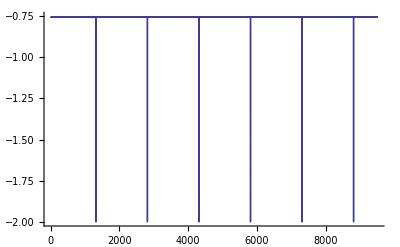

```mathematica
ListLinePlot[druhystlpec[[1;;9500;;1]],PlotRange->All]
```

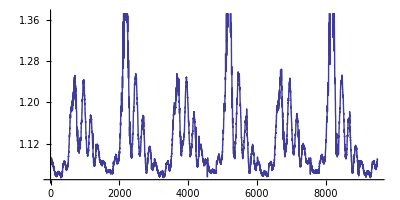

```mathematica
ListLinePlot[tretistlpec[[1;;9500;;1]],AspectRatio->0.5]
```

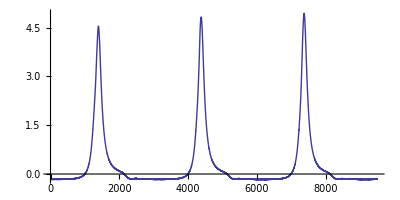

```mathematica
ListLinePlot[stvrtystlpec[[1;;9500;;1]], PlotRange->All,AspectRatio->0.5]
```

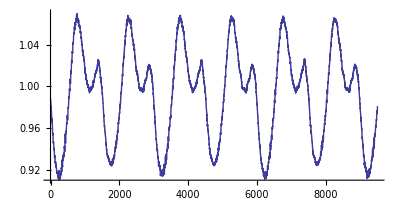

```mathematica
ListLinePlot[piatystlpec[[1;;9500;;1]], PlotRange->All,AspectRatio->0.5]
```

```mathematica
Length[prvystlpec]
```

1048576

```mathematica
pom3={};
Do[
If[druhystlpec[[i]]<-1.8,AppendTo[pom3, i]],{i,1,Length[druhystlpec]}];
pom4={};
Do[
If[pom3[[i+1]]-pom3[[i]]>10,AppendTo[pom4,pom3[[i]]]],{i,1, Length[pom3]-1}];
pom4
```

{1320,2817,4315,5812,7309,8806,10303,11800,13297,14794,16291,17789,19286,20783,22281,23777,25275,26772,28269,29766,31264,32761,34259,35757,37255,38753,40251,41749,43247,44745,46243,47740,49238,50736,52234,53731,55228,56725,58223,59720,61218,62715,64213,65710,67208,68705,70202,71699,73196,74693,76190,77687,79184,80680,82177,83674,85171,86667,88164,89661,91157,92654,94152,95648,97146,98643,100140,101637,103134,104631,106128,107625,109122,110620,112117,113614,115112,116609,118106,119603,121100,122597,124095,125592,127090,128587,130085,131582,133081,134579,136077,137575,139073,140570,142069,143566,145064,146561,148059,149557,151054,152551,154049,155546,157043,158540,160037,161534,163031,164527,166024,167521,169019,170516,172013,173510,175007,176504,178001,179498,180996,182492,183990,185487,186984,188480,189978,191475,192973,194470,195968,197465,198964,200461,201959,203456,204954,206451,207949,209446,210943,212440,213937,215433,216930,218427,219924,221421,222918,224415,225911,227408,228905,230401,231897,233393,234889,236385,237882,239377,240873,242369,243866,245361,246858,248353,249849,251345,252842,254338,255835,257331,258828,260324,261822,263319,264817,266314,267812,269309,270806,272304,273802,275299,276798,278295,279793,281291,282788,284286,285784,287282,288780,290277,291775,293272,294770,296267,297765,299262,300760,302257,303755,305252,306749,308247,309746,311244,312742,314240,315738,317236,318734,320232,321731,323228,324726,326224,327721,329219,330717,332214,333712,335210,336708,338205,339702,341199,342697,344193,345691,347188,348685,350181,351678,353175,354672,356168,357666,359162,360659,362156,363653,365149,366646,368143,369640,371136,372633,374130,375626,377123,378619,380115,381612,383109,384605,386102,387599,389095,390593,392089,393587,395084,396581,398079,399576,401074,402572,404069,405567,407065,408563,410060,411558,413056,414554,416052,417550,419047,420545,422042,423539,425036,426533,428030,429527,431023,432520,434017,435515,437011,438508,440005,441502,442999,444496,445993,447490,448987,450484,451980,453477,454974,456472,457969,459467,460963,462461,463958,465455,466952,468450,469946,471443,472940,474437,475933,477431,478928,480425,481921,483418,484915,486412,487908,489405,490901,492398,493895,495391,496888,498386,499883,501381,502878,504375,505872,507370,508868,510365,511863,513361,514858,516356,517853,519351,520849,522346,523844,525341,526839,528336,529833,531331,532828,534325,535823,537320,538817,540314,541811,543308,544805,546302,547799,549296,550793,552291,553788,555285,556782,558279,559776,561273,562770,564269,565766,567264,568761,570259,571756,573254,574751,576250,577747,579245,580743,582241,583738,585236,586734,588232,589729,591227,592725,594223,595720,597219,598716,600215,601712,603210,604707,606205,607702,609199,610696,612193,613690,615188,616685,618183,619680,621178,622675,624173,625670,627168,628665,630163,631660,633157,634654,636150,637647,639144,640641,642138,643635,645132,646628,648125,649622,651118,652615,654112,655609,657106,658603,660100,661597,663094,664591,666089,667585,669082,670579,672076,673573,675070,676567,678064,679560,681057,682554,684051,685548,687046,688542,690040,691536,693033,694530,696027,697524,699022,700518,702016,703513,705010,706506,708004,709500,710997,712494,713992,715489,716986,718484,719981,721478,722976,724473,725970,727467,728965,730462,731960,733457,734955,736452,737950,739447,740944,742441,743939,745435,746932,748429,749926,751423,752920,754417,755914,757411,758908,760405,761902,763399,764896,766393,767890,769387,770884,772381,773878,775374,776871,778367,779864,781361,782858,784354,785852,787348,788845,790341,791838,793335,794832,796328,797825,799322,800819,802316,803814,805311,806810,808307,809805,811302,812800,814297,815795,817292,818790,820287,821784,823281,824779,826276,827773,829270,830768,832265,833763,835260,836757,838254,839753,841250,842748,844245,845743,847240,848738,850235,851733,853230,854728,856225,857723,859220,860719,862216,863714,865212,866710,868208,869706,871203,872701,874199,875697,877194,878692,880189,881687,883184,884682,886179,887677,889174,890671,892169,893666,895163,896660,898157,899654,901150,902648,904145,905643,907140,908637,910134,911631,913127,914624,916121,917618,919114,920611,922107,923604,925100,926597,928094,929591,931088,932584,934081,935578,937074,938571,940067,941564,943061,944558,946054,947551,949047,950544,952041,953538,955035,956532,958029,959526,961023,962520,964017,965514,967011,968509,970006,971504,973001,974499,975996,977494,978991,980488,981986,983483,984980,986478,987976,989473,990971,992468,993965,995463,996960,998458,999956,1001455,1002953,1004451,1005949,1007448,1008946,1010444,1011942,1013440,1014938,1016436,1017933,1019432,1020929,1022428,1023926,1025425,1026923,1028422,1029920,1031419,1032916,1034415,1035912,1037411,1038909,1040407,1041904,1043403,1044900,1046397}

```mathematica
Length[pom4]
```

699

```mathematica
cyklus={};
Table[AppendTo[cyklus,tretistlpec[[pom4[[i]];;pom4[[i+2]]]]],{i,2,Length[pom4]-2,2}];
```

```mathematica
cyklus//Length
```

348

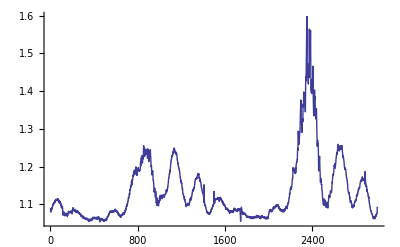
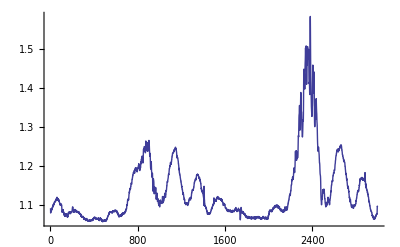
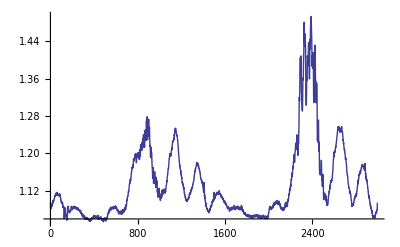
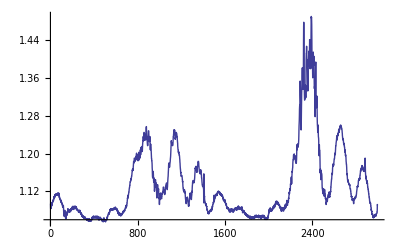
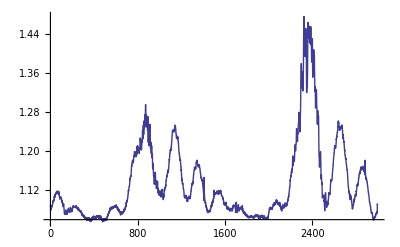
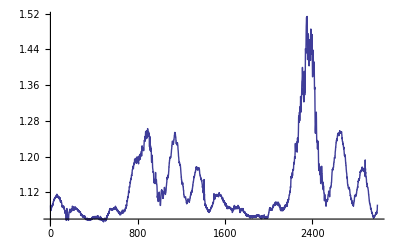
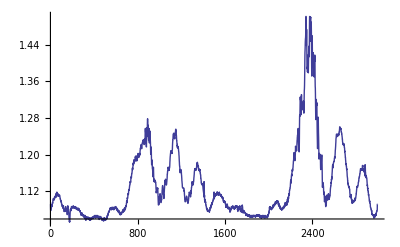
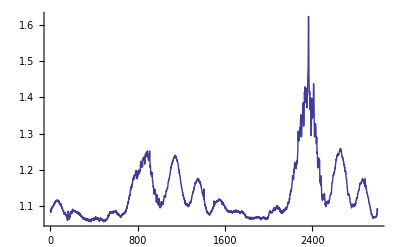

```mathematica
Table[ListLinePlot[cyklus[[i]],PlotRange->All],{i,1,10}]
```

```mathematica
Table[Length[cyklus[[i]]],{i,1,Length[cyklus]}]
```

{2996,2995,2995,2995,2996,2995,2995,2996,2995,2996,2997,2997,2997,2997,2996,2997,2996,2995,2996,2996,2996,2996,2995,2995,2995,2994,2995,2994,2995,2994,2995,2996,2995,2995,2995,2996,2995,2996,2995,2995,2996,2996,2996,2998,2997,2996,2997,2996,2997,2995,2996,2995,2995,2994,2995,2996,2995,2995,2995,2995,2996,2994,2996,2996,2996,2997,2996,2996,2996,2995,2994,2995,2995,2995,2994,2994,2993,2993,2993,2993,2993,2993,2993,2994,2994,2994,2996,2996,2996,2996,2996,2997,2997,2996,2997,2996,2996,2996,2996,2996,2996,2996,2998,2997,2997,2997,2997,2997,2996,2996,2997,2996,2995,2995,2996,2994,2995,2994,2995,2995,2994,2995,2994,2995,2994,2993,2995,2994,2994,2995,2996,2996,2996,2996,2997,2996,2997,2997,2996,2996,2995,2995,2994,2995,2995,2995,2995,2995,2995,2994,2995,2996,2995,2996,2995,2995,2995,2994,2996,2994,2995,2994,2994,2995,2994,2996,2996,2995,2997,2996,2996,2996,2997,2996,2996,2995,2996,2996,2995,2995,2995,2995,2995,2996,2995,2995,2995,2997,2996,2996,2996,2997,2997,2996,2997,2996,2997,2996,2997,2997,2996,2996,2995,2995,2996,2996,2996,2996,2996,2996,2995,2994,2995,2995,2994,2995,2994,2995,2995,2995,2995,2995,2995,2995,2995,2994,2995,2995,2995,2995,2995,2995,2995,2996,2994,2995,2995,2996,2996,2995,2996,2995,2996,2996,2996,2996,2995,2995,2995,2995,2995,2995,2995,2995,2995,2995,2995,2994,2994,2995,2994,2995,2994,2995,2994,2995,2995,2996,2997,2996,2996,2996,2996,2995,2996,2995,2996,2996,2995,2997,2996,2996,2996,2996,2996,2996,2997,2997,2997,2996,2997,2996,2996,2996,2996,2996,2996,2995,2995,2994,2996,2996,2995,2994,2995,2994,2994,2994,2995,2995,2994,2994,2994,2995,2994,2994,2995,2995,2995,2995,2995,2995,2996,2996,2996,2996,2996,2995,2997,2996,2995,2996,2997,2998,2997,2998,2997,2997,2996,2997,2998,2998,2998,2997,2997,2998,2996,2997}

```mathematica
pom5=Min[Table[Length[cyklus[[i]]],{i,1,Length[cyklus]}]];
pom6=Table[Take[cyklus[[i]],pom5],{i,1,Length[cyklus]}];
```

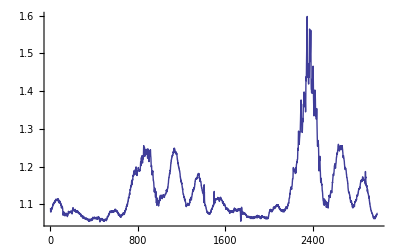
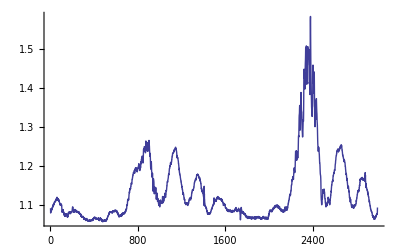
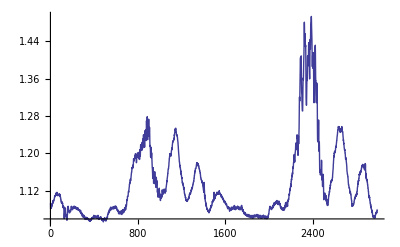
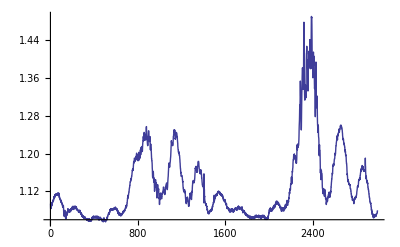
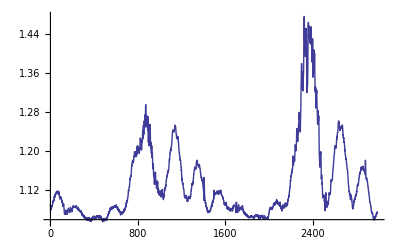
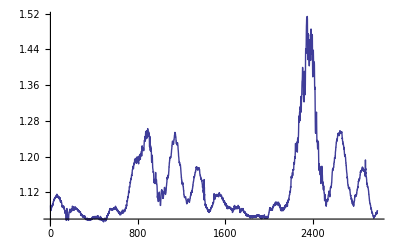
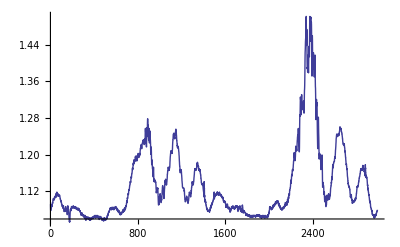
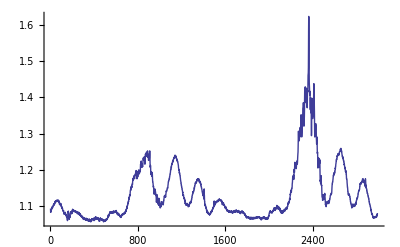

```mathematica
Table[ListLinePlot[pom6[[i]],PlotRange->All],{i,1,10}]
```

```mathematica
Transpose[pom6]//Dimensions
```

{2993,348}

```mathematica
priemernehodnotydruhystlpec=Table[Mean[pom6[[All,i]]],{i,1,2993}];
```

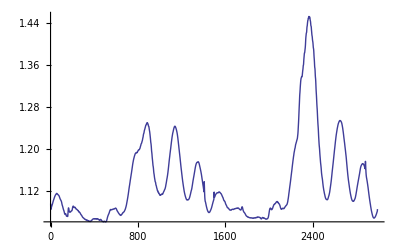

```mathematica
ListLinePlot[priemernehodnotydruhystlpec]
```

```mathematica
cyklus3={};
cyklus4={};
cyklus5={};
Table[AppendTo[cyklus3,tretistlpec[[pom4[[i]];;pom4[[i+2]]]]],{i,2,Length[pom4]-2,2}];
Table[AppendTo[cyklus4,stvrtystlpec[[pom4[[i]];;pom4[[i+2]]]]],{i,2,Length[pom4]-2,2}];
Table[AppendTo[cyklus5,piatystlpec[[pom4[[i]];;pom4[[i+2]]]]],{i,2,Length[pom4]-2,2}];
```

```mathematica
cyklus3//Length
```

348

```mathematica
Table[ListLinePlot[cyklus3[[i]],PlotRange->All],{i,1,10}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

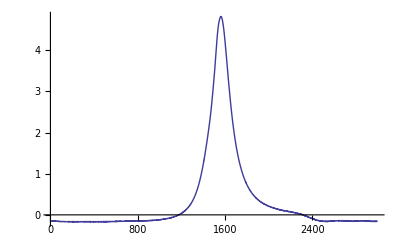
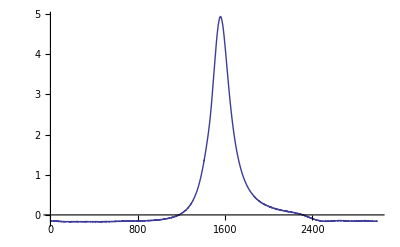
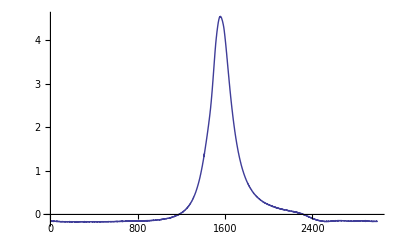
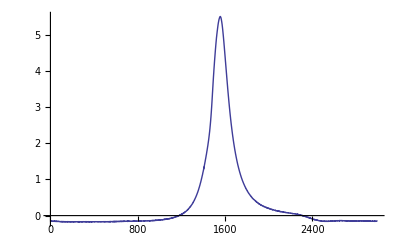
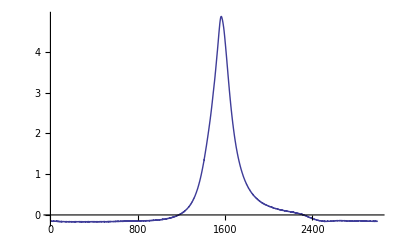
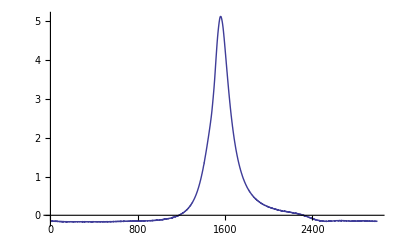
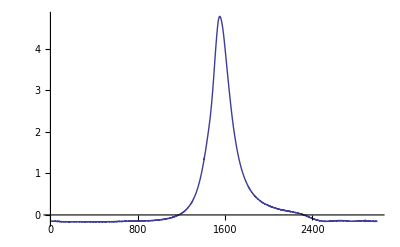
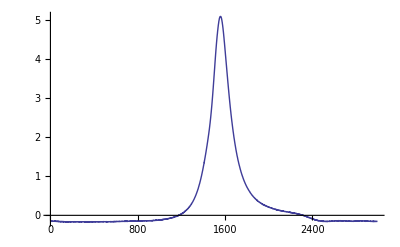

```mathematica
Table[ListLinePlot[cyklus4[[i]],PlotRange->All],{i,1,10}]
```

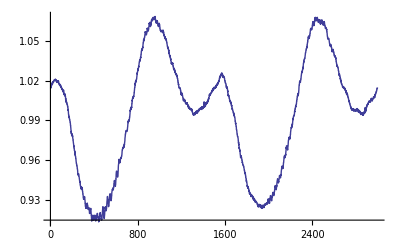
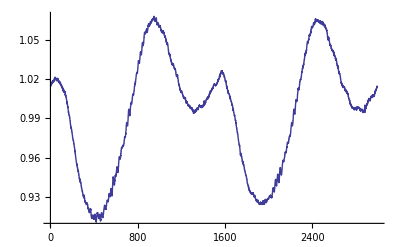
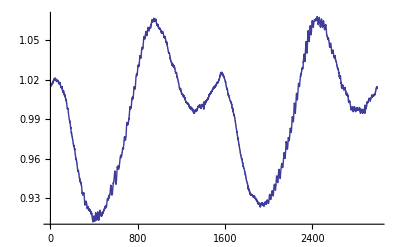
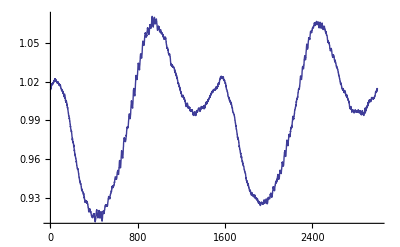
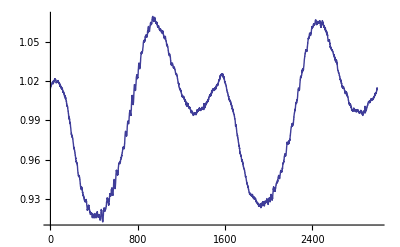
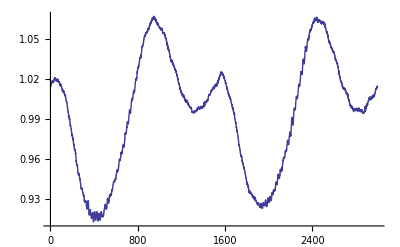
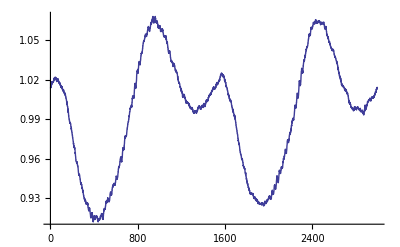
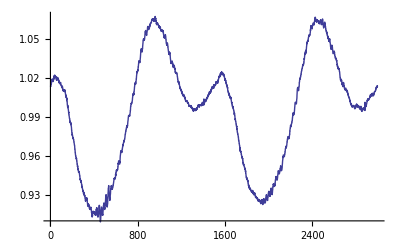

```mathematica
Table[ListLinePlot[cyklus5[[i]],PlotRange->All],{i,1,10}]
```

```mathematica
Table[Length[cyklus3[[i]]],{i,1,Length[cyklus]}]
```

{2996,2995,2995,2995,2996,2995,2995,2996,2995,2996,2997,2997,2997,2997,2996,2997,2996,2995,2996,2996,2996,2996,2995,2995,2995,2994,2995,2994,2995,2994,2995,2996,2995,2995,2995,2996,2995,2996,2995,2995,2996,2996,2996,2998,2997,2996,2997,2996,2997,2995,2996,2995,2995,2994,2995,2996,2995,2995,2995,2995,2996,2994,2996,2996,2996,2997,2996,2996,2996,2995,2994,2995,2995,2995,2994,2994,2993,2993,2993,2993,2993,2993,2993,2994,2994,2994,2996,2996,2996,2996,2996,2997,2997,2996,2997,2996,2996,2996,2996,2996,2996,2996,2998,2997,2997,2997,2997,2997,2996,2996,2997,2996,2995,2995,2996,2994,2995,2994,2995,2995,2994,2995,2994,2995,2994,2993,2995,2994,2994,2995,2996,2996,2996,2996,2997,2996,2997,2997,2996,2996,2995,2995,2994,2995,2995,2995,2995,2995,2995,2994,2995,2996,2995,2996,2995,2995,2995,2994,2996,2994,2995,2994,2994,2995,2994,2996,2996,2995,2997,2996,2996,2996,2997,2996,2996,2995,2996,2996,2995,2995,2995,2995,2995,2996,2995,2995,2995,2997,2996,2996,2996,2997,2997,2996,2997,2996,2997,2996,2997,2997,2996,2996,2995,2995,2996,2996,2996,2996,2996,2996,2995,2994,2995,2995,2994,2995,2994,2995,2995,2995,2995,2995,2995,2995,2995,2994,2995,2995,2995,2995,2995,2995,2995,2996,2994,2995,2995,2996,2996,2995,2996,2995,2996,2996,2996,2996,2995,2995,2995,2995,2995,2995,2995,2995,2995,2995,2995,2994,2994,2995,2994,2995,2994,2995,2994,2995,2995,2996,2997,2996,2996,2996,2996,2995,2996,2995,2996,2996,2995,2997,2996,2996,2996,2996,2996,2996,2997,2997,2997,2996,2997,2996,2996,2996,2996,2996,2996,2995,2995,2994,2996,2996,2995,2994,2995,2994,2994,2994,2995,2995,2994,2994,2994,2995,2994,2994,2995,2995,2995,2995,2995,2995,2996,2996,2996,2996,2996,2995,2997,2996,2995,2996,2997,2998,2997,2998,2997,2997,2996,2997,2998,2998,2998,2997,2997,2998,2996,2997}

```mathematica
pom5=Min[Table[Length[cyklus3[[i]]],{i,1,Length[cyklus3]}]];
cyklus3orezany=Table[Take[cyklus3[[i]],pom5],{i,1,Length[cyklus3]}];
cyklus4orezany=Table[Take[cyklus4[[i]],pom5],{i,1,Length[cyklus3]}];
cyklus5orezany=Table[Take[cyklus5[[i]],pom5],{i,1,Length[cyklus3]}];
```

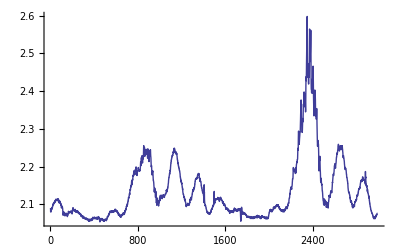
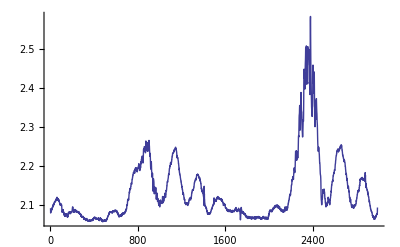
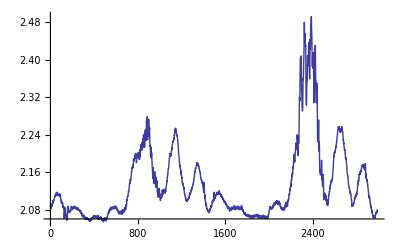
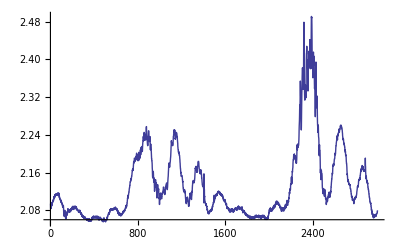
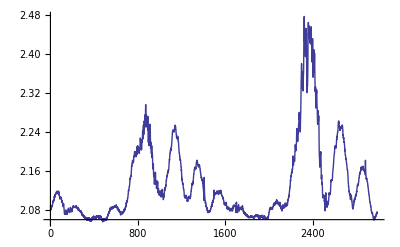
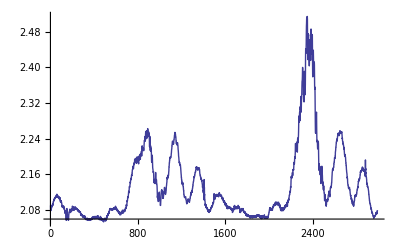
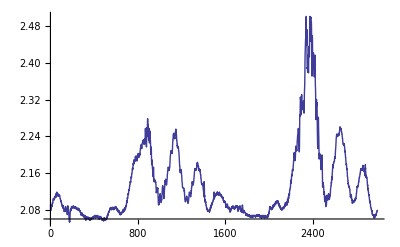
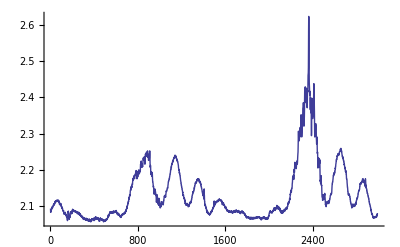

```mathematica
Table[ListLinePlot[cyklus3orezany[[i]]+1,PlotRange->All],{i,1,10}]
```

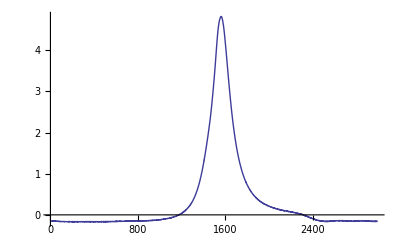
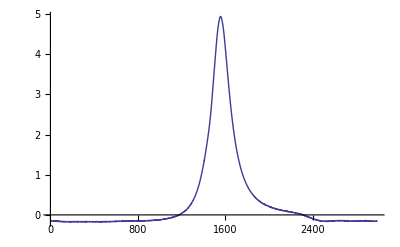
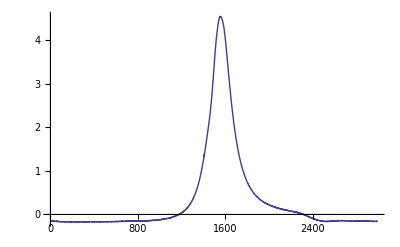
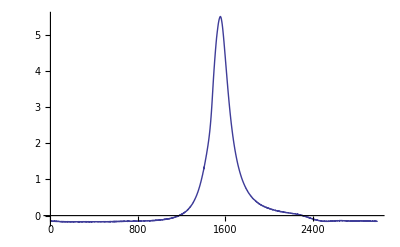
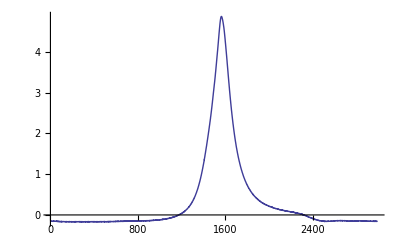
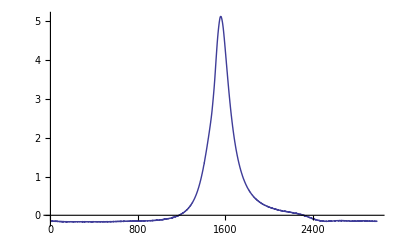
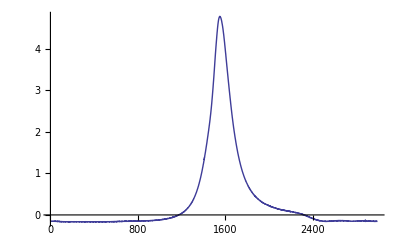
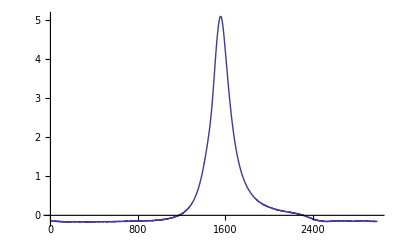

```mathematica
Table[ListLinePlot[cyklus4orezany[[i]],PlotRange->All],{i,1,10}]
```

```mathematica
Transpose[cyklus3orezany]//Dimensions
```

{2993,348}

```mathematica
priemernehodnoty3stlpec=Table[Mean[cyklus3orezany[[All,i]]],{i,1,2993}];
priemernehodnoty4stlpec=Table[Mean[cyklus4orezany[[All,i]]],{i,1,2993}];
priemernehodnoty5stlpec=Table[Mean[cyklus5orezany[[All,i]]],{i,1,2993}];
```

```mathematica
Length[priemernehodnoty4stlpec]
```

2993

```mathematica
k=0;
x=Table[k=k+720/Length[priemernehodnoty4stlpec]//N,{Length[priemernehodnoty4stlpec]}];
```

```mathematica
obr3=ListLinePlot[priemernehodnoty3stlpec]
```

-Graphics-

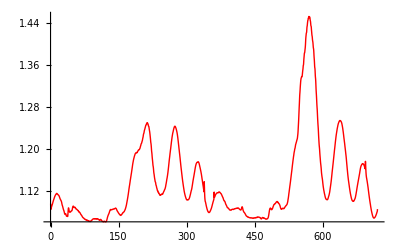

```mathematica
dataobr3=Transpose@{x,priemernehodnoty3stlpec};
obr3a2000=ListLinePlot[dataobr3,PlotStyle->Red]
```

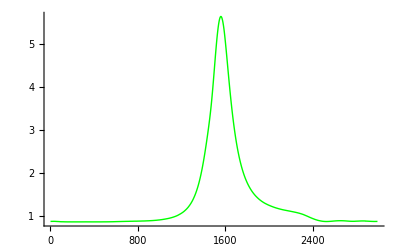

```mathematica
obr4=ListLinePlot[priemernehodnoty4stlpec+1.0335, PlotStyle->Green,PlotRange->All]
```

```mathematica
priemernehodnoty4stlpecnove=priemernehodnoty4stlpec+1.1335;
```

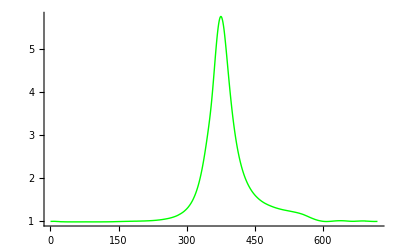

```mathematica
dataobr4=Transpose@{x,priemernehodnoty4stlpecnove};
obr2000va=ListLinePlot[dataobr4,PlotStyle->Green,PlotRange->All]
```

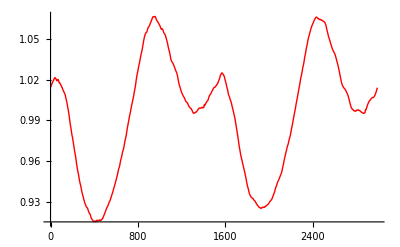

```mathematica
obr5=ListLinePlot[priemernehodnoty5stlpec,PlotStyle->Red]
```

-Graphics-

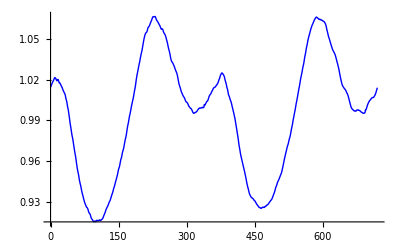

```mathematica
-Graphics-
dataobr5=Transpose@{x,priemernehodnoty5stlpec};
obr2000a=ListLinePlot[dataobr5,PlotStyle->Blue]
```

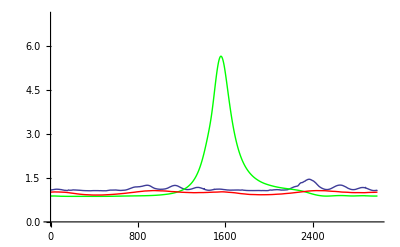

```mathematica
Show[{obr3,obr4,obr5},PlotRange->{{0,2993},{0,7}},AxesOrigin->{0,0}]
```

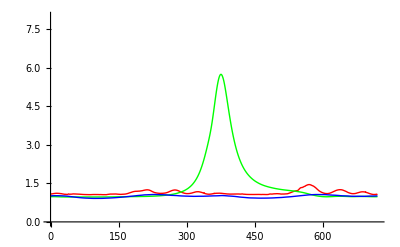

```mathematica
obrfinala=GraphicsGrid[{{obr3a,obr4a,obr5a}},ImageSize->{1000,250}];
Show[{obr3a,obr4a,obr5a},PlotRange->{{0,720},{0,8}},AxesOrigin->{0,0}]
```

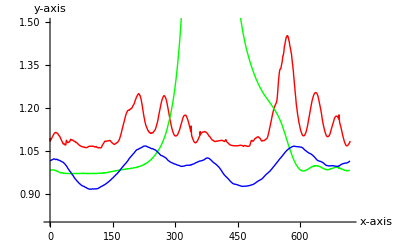

```mathematica
brfinaladetail=GraphicsGrid[{{obr3a,obr4a,obr5a}},ImageSize->{1000,250}];
Show[{obr3a,obr4a,obr5a},PlotRange->{{0,720},{0.8,1.5}},AxesOrigin->{0,0.8},LabelStyle->(FontSize->14),AxesLabel->{"x-axis","y-axis"}]
```

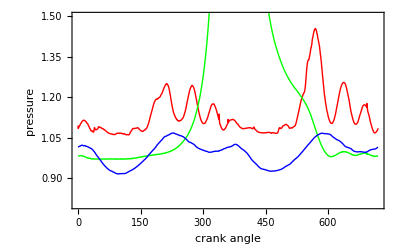

```mathematica
obrfinaladetail=GraphicsGrid[{{obr3a,obr4a,obr5a}},ImageSize->{1000,250}];
Show[{obr3a,obr4a,obr5a},PlotRange->{{0,720},{0.8,1.5}},AxesOrigin->{0,0.8},PlotRange->{{-3,0},{0,1}},Frame->True,FrameLabel->{"crank angle","pressure"},LabelStyle->(FontSize->16)]
```

```mathematica
Show[{obr3a,obr4a,obr5a},PlotRange->{{0,720},{0.8,1.5}},AxesOrigin->{0,0.8},Frame->True,FrameLabel->{"crank angle","pressure"},LabelStyle->(FontSize->16)]
```

-Graphics-